```mathematica
nthRootsExponential[z_,n_]:=Module[{r,θ},r=Abs[z]^(1/n);
θ=N[Arg[z]];(*Get numerical value once*)(*Convert to exact fraction of π if possible*)θ=If[Abs[θ/π-Round[θ/π]]<10^(-10),Round[θ/π]*π,θ];
Table[r*Exp[I*(θ/n+2π*k/n)],{k,0,n-1}]]

Solve[z1^4 ==-4,z1]
```

{{z1→-(-1)^(1/4) √2},{z1→(-1)^(1/4) √2},{z1→-(-1)^(3/4) √2},{z1→(-1)^(3/4) √2}}

```mathematica
Roots[z1^4+4==0,z1]
```

z1==(-1)^(3/4) √2||z1==-(-1)^(1/4) √2||z1==-(-1)^(3/4) √2||z1==(-1)^(1/4) √2

{{w→-2 (-1)^(1/4)},{w→2 (-1)^(1/4)},{w→-2 (-1)^(3/4)},{w→2 (-1)^(3/4)}}

{2 (-1)^(1/4),2 (-1)^(3/4),-2 (-1)^(1/4),-2 (-1)^(3/4)}

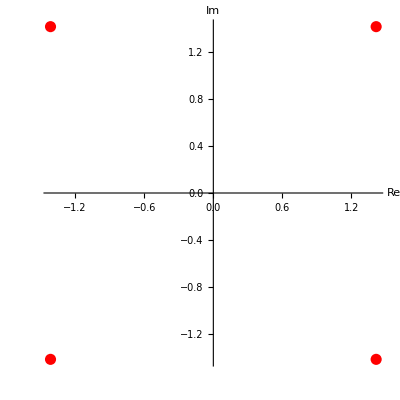

```mathematica
z = -16;
n = 1/4;
Solve[w^n==z,w]
(*or*)
roots=Table[(z)^(1/n)*Exp[2 π I k/n],{k,0,n-1}]

ListPlot[{Re[#],Im[#]}&/@roots,PlotStyle->{Red,PointSize[0.02]},AspectRatio->1,AxesLabel->{"Re","Im"},PlotRange->All]
```

```mathematica
Manipulate[Module[{roots,radius,coords},roots=Table[z^(1/n)*Exp[2 π I k/n],{k,0,n-1}];
radius=Abs[z];
coords={Re[#],Im[#]}&/@roots;
Graphics[{{Gray,Dashed,Circle[{0,0},radius]},{Blue,Line[Append[coords,First[coords]]]},{Red,PointSize[0.02],Point[coords]},{Thin,Gray,Line[{{0,0},#}]&/@coords}},Axes->True,AspectRatio->1,AxesLabel->{"Re","Im"},PlotRange->1.2*radius*{{-1,1},{-1,1}},GridLines->Automatic]],{{z1,z,"Complex number"},-10-10*I,10+10*I},{{n,4,"Root index"},1,24,1}]
```

```mathematica
(*Convert to exponential form*)exponentialRoots=Table[Abs[roots[[k]]]*Exp[I*Arg[roots[[k]]]],{k,1,Length[roots]}]
```

{2 ⅇ^(-(ⅈ π)/6),2 ⅇ^(ⅈ Arg[ⅈ (-1-ⅈ √3)^(1/4)]),2 ⅇ^(ⅈ Arg[-(-1-ⅈ √3)^(1/4)]),2 ⅇ^(ⅈ Arg[-ⅈ (-1-ⅈ √3)^(1/4)])}

```mathematica
theRoots = nthRootsExponential[z,4]
Arg[theRoots]*180/Pi
```

{1.73205-1. ⅈ,1.+1.73205 ⅈ,-1.73205+1. ⅈ,-1.-1.73205 ⅈ}

{-30.,60.,150.,-120.}